```mathematica
1/(1 Giga ElectronVolt*)
```

```mathematica
Solve[(γ-1)*10^9==10^-2,γ]
```

{{γ→100000000001/100000000000}}

```mathematica
Solve[100000000001/100000000000==1/Sqrt[1-β^2],β]//N
```

{{β→-4.47214×10^-6},{β→4.47214×10^-6}}

```mathematica
1/(1 Giga ElectronVolt*4.472135954966038*^-5*100000000001/100000000000)
```

22360.7/(ElectronVolt Giga)

```mathematica
Convert[22360.679774942/(ElectronVolt Giga)*200 Mega ElectronVolt*Fermi,Angstrom]//N
```

0.0447214 Angstrom

```mathematica
Solve[(γ-1)*1000==En,γ]
```

{{γ→(1000+En)/1000}}

```mathematica
Solve[(1000+En)/1000==1/Sqrt[1-β^2],β]//N
```

{{β→(√En √(2000.+En))/(-1000.-1. En)},{β→(√En √(2000.+En))/(1000.+En)}}

```mathematica
(√En √(2000.+En))/(1000.+En)/.En->1
```

0.0446879

```mathematica
1/(1000*((1000+En)/1000)((√En √(2000.+En))/(1000.+En)))*200*Fermi
```

```mathematica
Convert[(200 (1000.+En) Fermi)/(√En (1000+En) √(2000.+En)),Angstrom]/Angstrom
```

(1000.+En)/(500 √En (1000+En) √(2000.+En))

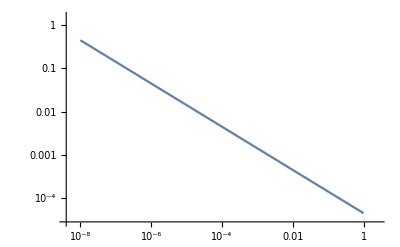

```mathematica
LogLogPlot[(1000.+En)/(500 √En (1000+En) √(2000.+En)),{En,10^-8,1}]
```

```mathematica
36*1/137*(0.8(Mega ElectronVolt)^3)^(-1/3)
```

0.283064/((ElectronVolt^3 Mega^3)^(1/3))

```mathematica
(0.8)^(-1/3)
```

1.07722

```mathematica
Convert[1.077217345015942/(Mega ElectronVolt)*Mega ElectronVolt*200 Fermi,Fermi]
```

215.443 Fermi

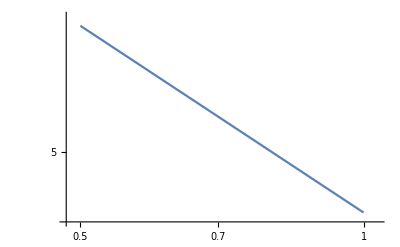

```mathematica
LogLogPlot[(200 (1000.+En))/(√En (1000+En) √(2000.+En)),{En,0.5,1}]
```

```mathematica
Solve[{m*vi^2==m*vf^2+M*v^2,m*vi==m*vf*Cos[θ]+M*v*Cos[ψ],0==m*vf*Sin[θ]-M*v*Sin[ψ]},vf,{ψ,v}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{vf→(2 m vi Cos[θ]-√2 √(-m^2 vi^2+2 M^2 vi^2+m^2 vi^2 Cos[2 θ]))/(2 (M+m Cos[θ]^2+m Sin[θ]^2))},{vf→(2 m vi Cos[θ]+√2 √(-m^2 vi^2+2 M^2 vi^2+m^2 vi^2 Cos[2 θ]))/(2 (M+m Cos[θ]^2+m Sin[θ]^2))}}

```mathematica
{m*vi^2==m*vf^2+M*v^2,m*vi==m*vf*Cos[θ]+M*v*Cos[ψ],0==m*vf*Sin[θ]-M*v*Sin[ψ]}/.{θ->0,ψ->0}
```

{m vi^2==M v^2+m vf^2,m vi==M v+m vf,True}

```mathematica
Solve[{m vi^2==M v^2+m vf^2,m vi==M v+m vf},vf,v]//FullSimplify
```

Solve::bdomv: Warning: v is not a valid domain specification. Assuming it is a variable to eliminate.

{{vf→vi},{vf→((m-M) vi)/(m+M)}}

```mathematica
(2 m vi Cos[θ]+√2 √(-m^2 vi^2+2 M^2 vi^2+m^2 vi^2 Cos[2 θ]))/(2 (M+m Cos[θ]^2+m Sin[θ]^2))/.θ->Pi//FullSimplify
```

(-m vi+√(M^2 vi^2))/(m+M)

```mathematica
(2 m vi Cos[θ]+√2 √(-m^2 vi^2+2 M^2 vi^2+m^2 vi^2 Cos[2 θ]))/(2 (M+m Cos[θ]^2+m Sin[θ]^2))/.θ->0//FullSimplify
```

(m vi+√(M^2 vi^2))/(m+M)

```mathematica
1/4((12-1)/(12+1))^2//N
```

0.178994

```mathematica
(2*10^6)/1
```

2000000

```mathematica
Log[1/5]/Log[0.8520710059171598]//N
```

10.0536

```mathematica
Convert[1/(Barn*10^32/Centimeter^3),Centimeter]//N
```

1.×10^-8 Centimeter

```mathematica
((M-m)/(M+m)+1)/2//FullSimplify
```

```mathematica
(M/(m+M))^2/.{M->12000,m->1000}//N
```

0.852071

```mathematica
Log[1/10]/Log[0.8520710059171598]
```

14.3835

```mathematica
Solve[(1-0.8520710059171598)*x==0.1,x]
```

{{x→0.676}}

#### Energy transfer given by α parameter

```mathematica
(1-(M/(m+M))^2)/.{M->12000,m->1000}//N
```

0.147929

#### Below ~1 MeV neutron kinetic energy, elastic scattering may be complicated by lattice effects. So go from ~10 MeV - 1 MeV

```mathematica
Log[1/5]/Log[0.8520710059171598]
```

10.0536

#### Total distance.

```mathematica
Convert[Sqrt[10]/(Barn*10^32/Centimeter^3),Centimeter]//N
```

3.16228×10^-8 Centimeter

```mathematica
10^-7*Centimeter Log[10^6/10]/Log[5]//N
```

7.15338×10^-7 Centimeter